```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==6 &&Greater[ Length[FindClique[g,{4}]],0]
]&]
```

{28764,27246,22708,9490,364}

```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==3 &&Greater[ Length[FindClique[g,{3}]],0]
]&]
```

{26487,21951,20439,8757,7293,2917,333,273,109,13}

```mathematica
FindClique[allGraphs5[K5Key,"graph"]]
```

{{1,2,3,4,5}}

```mathematica
allGraphs5[28764,"graph"]
```

-Graphics-

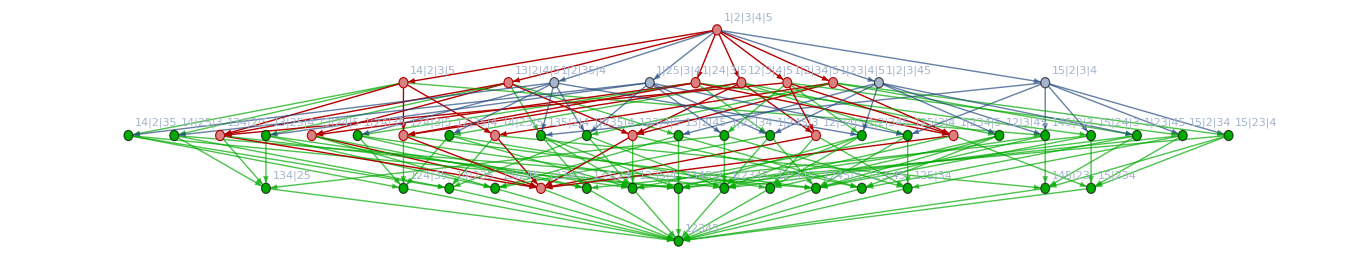

```mathematica
MobiusGraphDoubleGreen[K5Key,28764,allGraphs5]
```

```mathematica
StirlingS2[4,3]
```

6

```mathematica
StirlingS2[5,4]
```

10

```mathematica
allGraphs5[7293,"graph"]
```

-Graphics-

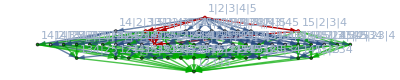

```mathematica
MobiusGraphDoubleGreen[K5Key,7293,allGraphs5]
```

```mathematica
StirlingS2[5,3]
```

25

```mathematica
Binomial[4,2]
```

6

```mathematica
StirlingS2[3,2]*2^Binomial[4,2]
```

24

```mathematica
TableForm[Table[{StirlingS2[n,n-1]-StirlingS2[n-1,n-2],StirlingS2[n,n-2]},{n,2,6}]]
```

1 | 0
2 | 1
3 | 7
4 | 25
5 | 65

```mathematica
Simplify[StirlingS2[n,n-1]-StirlingS2[n-1,n-2]]
```

-StirlingS2[-1+n,-2+n]+StirlingS2[n,-1+n]

```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==5 &&EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->1]&&EdgeQ[g,1<->3]
]&]
```

{28683}

```mathematica
allGraphs5[28683,"graph"]
```

-Graphics-

```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==6 &&EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->1]&&EdgeQ[g,1<->3]&&EdgeQ[g,2<->4]
]&]
```

{28764}

```mathematica
allGraphs5[28764,"graph"]
```

-Graphics-

```mathematica
ChromaticPolynomial[allGraphs5[28764,"graph"],x]
```

-6 x^2+11 x^3-6 x^4+x^5

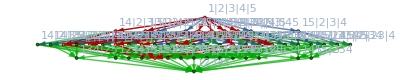

```mathematica
MobiusGraphDoubleGreen[K5Key,28764,allGraphs5]
```

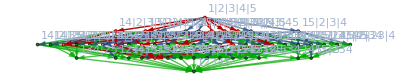

```mathematica
MobiusGraphDoubleGreen[K5Key,28683,allGraphs5]
```

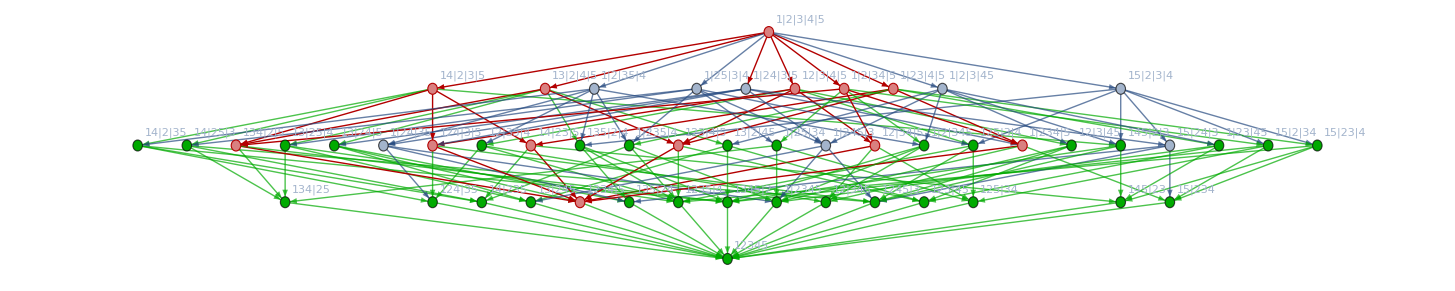

```mathematica
Graph[MobiusGraphDoubleGreen[K5Key,28683,allGraphs5],GraphHighlight->{n1x2x3x4x5->n1x24x3x5}]
```

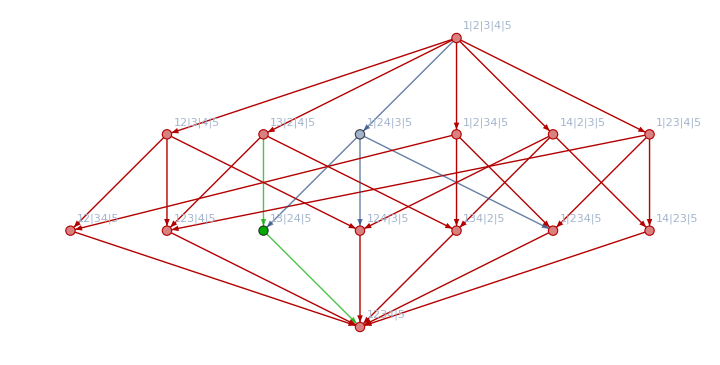

```mathematica
Graph[MobiusGraphDoubleGreen[28764,28683,allGraphs5]]
```

```mathematica
Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},VertexCount[g]==6&&EdgeCount[g]==10]&]
```

{7174332,7174170,7174116,7174098,7174092,7174090,7173684,7173630,7173612,7173606,7173604,7173468,7173450,7173444,7173442,7173396,7173390,7173388,7173372,7173370,7173364,7172226,7172172,7172154,7172148,7172146,7172010,7171992,7171986,7171984,7171938,7171932,7171930,7171914,7171912,7171906,7171524,7171506,7171500,7171498,7171452,7171446,7171444,7171428,7171426,7171420,7171290,7171284,7171282,7171266,7171264,7171258,7171212,7171210,7171204,7171186,7167852,7167798,7167780,7167774,7167772,7167636,7167618,7167612,7167610,7167564,7167558,7167556,7167540,7167538,7167532,7167150,7167132,7167126,7167124,7167078,7167072,7167070,7167054,7167052,7167046,7166916,7166910,7166908,7166892,7166890,7166884,7166838,7166836,7166830,7166812,7165692,7165674,7165668,7165666,7165620,7165614,7165612,7165596,7165594,7165588,7165458,7165452,7165450,7165434,7165432,7165426,7165380,7165378,7165372,7165354,7164972,7164966,7164964,7164948,7164946,7164940,7164894,7164892,7164886,7164868,7164732,7164730,7164724,7164706,7164652,7154730,7154676,7154658,7154652,7154650,7154514,7154496,7154490,7154488,7154442,7154436,7154434,7154418,7154416,7154410,7154028,7154010,7154004,7154002,7153956,7153950,7153948,7153932,7153930,7153924,7153794,7153788,7153786,7153770,7153768,7153762,7153716,7153714,7153708,7153690,7152570,7152552,7152546,7152544,7152498,7152492,7152490,7152474,7152472,7152466,7152336,7152330,7152328,7152312,7152310,7152304,7152258,7152256,7152250,7152232,7151850,7151844,7151842,7151826,7151824,7151818,7151772,7151770,7151764,7151746,7151610,7151608,7151602,7151584,7151530,7148196,7148178,7148172,7148170,7148124,7148118,7148116,7148100,7148098,7148092,7147962,7147956,7147954,7147938,7147936,7147930,7147884,7147882,7147876,7147858,7147476,7147470,7147468,7147452,7147450,7147444,7147398,7147396,7147390,7147372,7147236,7147234,7147228,7147210,7147156,7146018,7146012,7146010,7145994,7145992,7145986,7145940,7145938,7145932,7145914,7145778,7145776,7145770,7145752,7145698,7145292,7145290,7145284,7145266,7145212,7145050,7115364,7115310,7115292,7115286,7115284,7115148,7115130,7115124,7115122,7115076,7115070,7115068,7115052,7115050,7115044,7114662,7114644,7114638,7114636,7114590,7114584,7114582,7114566,7114564,7114558,7114428,7114422,7114420,7114404,7114402,7114396,7114350,7114348,7114342,7114324,7113204,7113186,7113180,7113178,7113132,7113126,7113124,7113108,7113106,7113100,7112970,7112964,7112962,7112946,7112944,7112938,7112892,7112890,7112884,7112866,7112484,7112478,7112476,7112460,7112458,7112452,7112406,7112404,7112398,7112380,7112244,7112242,7112236,7112218,7112164,7108830,7108812,7108806,7108804,7108758,7108752,7108750,7108734,7108732,7108726,7108596,7108590,7108588,7108572,7108570,7108564,7108518,7108516,7108510,7108492,7108110,7108104,7108102,7108086,7108084,7108078,7108032,7108030,7108024,7108006,7107870,7107868,7107862,7107844,7107790,7106652,7106646,7106644,7106628,7106626,7106620,7106574,7106572,7106566,7106548,7106412,7106410,7106404,7106386,7106332,7105926,7105924,7105918,7105900,7105846,7105684,7095708,7095690,7095684,7095682,7095636,7095630,7095628,7095612,7095610,7095604,7095474,7095468,7095466,7095450,7095448,7095442,7095396,7095394,7095388,7095370,7094988,7094982,7094980,7094964,7094962,7094956,7094910,7094908,7094902,7094884,7094748,7094746,7094740,7094722,7094668,7093530,7093524,7093522,7093506,7093504,7093498,7093452,7093450,7093444,7093426,7093290,7093288,7093282,7093264,7093210,7092804,7092802,7092796,7092778,7092724,7092562,7089156,7089150,7089148,7089132,7089130,7089124,7089078,7089076,7089070,7089052,7088916,7088914,7088908,7088890,7088836,7088430,7088428,7088422,7088404,7088350,7088188,7086972,7086970,7086964,7086946,7086892,7086730,7086244,6997266,6997212,6997194,6997188,6997186,6997050,6997032,6997026,6997024,6996978,6996972,6996970,6996954,6996952,6996946,6996564,6996546,6996540,6996538,6996492,6996486,6996484,6996468,6996466,6996460,6996330,6996324,6996322,6996306,6996304,6996298,6996252,6996250,6996244,6996226,6995106,6995088,6995082,6995080,6995034,6995028,6995026,6995010,6995008,6995002,6994872,6994866,6994864,6994848,6994846,6994840,6994794,6994792,6994786,6994768,6994386,6994380,6994378,6994362,6994360,6994354,6994308,6994306,6994300,6994282,6994146,6994144,6994138,6994120,6994066,6990732,6990714,6990708,6990706,6990660,6990654,6990652,6990636,6990634,6990628,6990498,6990492,6990490,6990474,6990472,6990466,6990420,6990418,6990412,6990394,6990012,6990006,6990004,6989988,6989986,6989980,6989934,6989932,6989926,6989908,6989772,6989770,6989764,6989746,6989692,6988554,6988548,6988546,6988530,6988528,6988522,6988476,6988474,6988468,6988450,6988314,6988312,6988306,6988288,6988234,6987828,6987826,6987820,6987802,6987748,6987586,6977610,6977592,6977586,6977584,6977538,6977532,6977530,6977514,6977512,6977506,6977376,6977370,6977368,6977352,6977350,6977344,6977298,6977296,6977290,6977272,6976890,6976884,6976882,6976866,6976864,6976858,6976812,6976810,6976804,6976786,6976650,6976648,6976642,6976624,6976570,6975432,6975426,6975424,6975408,6975406,6975400,6975354,6975352,6975346,6975328,6975192,6975190,6975184,6975166,6975112,6974706,6974704,6974698,6974680,6974626,6974464,6971058,6971052,6971050,6971034,6971032,6971026,6970980,6970978,6970972,6970954,6970818,6970816,6970810,6970792,6970738,6970332,6970330,6970324,6970306,6970252,6970090,6968874,6968872,6968866,6968848,6968794,6968632,6968146,6938244,6938226,6938220,6938218,6938172,6938166,6938164,6938148,6938146,6938140,6938010,6938004,6938002,6937986,6937984,6937978,6937932,6937930,6937924,6937906,6937524,6937518,6937516,6937500,6937498,6937492,6937446,6937444,6937438,6937420,6937284,6937282,6937276,6937258,6937204,6936066,6936060,6936058,6936042,6936040,6936034,6935988,6935986,6935980,6935962,6935826,6935824,6935818,6935800,6935746,6935340,6935338,6935332,6935314,6935260,6935098,6931692,6931686,6931684,6931668,6931666,6931660,6931614,6931612,6931606,6931588,6931452,6931450,6931444,6931426,6931372,6930966,6930964,6930958,6930940,6930886,6930724,6929508,6929506,6929500,6929482,6929428,6929266,6928780,6918570,6918564,6918562,6918546,6918544,6918538,6918492,6918490,6918484,6918466,6918330,6918328,6918322,6918304,6918250,6917844,6917842,6917836,6917818,6917764,6917602,6916386,6916384,6916378,6916360,6916306,6916144,6915658,6912012,6912010,6912004,6911986,6911932,6911770,6911284,6909826,6642972,6642918,6642900,6642894,6642892,6642756,6642738,6642732,6642730,6642684,6642678,6642676,6642660,6642658,6642652,6642270,6642252,6642246,6642244,6642198,6642192,6642190,6642174,6642172,6642166,6642036,6642030,6642028,6642012,6642010,6642004,6641958,6641956,6641950,6641932,6640812,6640794,6640788,6640786,6640740,6640734,6640732,6640716,6640714,6640708,6640578,6640572,6640570,6640554,6640552,6640546,6640500,6640498,6640492,6640474,6640092,6640086,6640084,6640068,6640066,6640060,6640014,6640012,6640006,6639988,6639852,6639850,6639844,6639826,6639772,6636438,6636420,6636414,6636412,6636366,6636360,6636358,6636342,6636340,6636334,6636204,6636198,6636196,6636180,6636178,6636172,6636126,6636124,6636118,6636100,6635718,6635712,6635710,6635694,6635692,6635686,6635640,6635638,6635632,6635614,6635478,6635476,6635470,6635452,6635398,6634260,6634254,6634252,6634236,6634234,6634228,6634182,6634180,6634174,6634156,6634020,6634018,6634012,6633994,6633940,6633534,6633532,6633526,6633508,6633454,6633292,6623316,6623298,6623292,6623290,6623244,6623238,6623236,6623220,6623218,6623212,6623082,6623076,6623074,6623058,6623056,6623050,6623004,6623002,6622996,6622978,6622596,6622590,6622588,6622572,6622570,6622564,6622518,6622516,6622510,6622492,6622356,6622354,6622348,6622330,6622276,6621138,6621132,6621130,6621114,6621112,6621106,6621060,6621058,6621052,6621034,6620898,6620896,6620890,6620872,6620818,6620412,6620410,6620404,6620386,6620332,6620170,6616764,6616758,6616756,6616740,6616738,6616732,6616686,6616684,6616678,6616660,6616524,6616522,6616516,6616498,6616444,6616038,6616036,6616030,6616012,6615958,6615796,6614580,6614578,6614572,6614554,6614500,6614338,6613852,6583950,6583932,6583926,6583924,6583878,6583872,6583870,6583854,6583852,6583846,6583716,6583710,6583708,6583692,6583690,6583684,6583638,6583636,6583630,6583612,6583230,6583224,6583222,6583206,6583204,6583198,6583152,6583150,6583144,6583126,6582990,6582988,6582982,6582964,6582910,6581772,6581766,6581764,6581748,6581746,6581740,6581694,6581692,6581686,6581668,6581532,6581530,6581524,6581506,6581452,6581046,6581044,6581038,6581020,6580966,6580804,6577398,6577392,6577390,6577374,6577372,6577366,6577320,6577318,6577312,6577294,6577158,6577156,6577150,6577132,6577078,6576672,6576670,6576664,6576646,6576592,6576430,6575214,6575212,6575206,6575188,6575134,6574972,6574486,6564276,6564270,6564268,6564252,6564250,6564244,6564198,6564196,6564190,6564172,6564036,6564034,6564028,6564010,6563956,6563550,6563548,6563542,6563524,6563470,6563308,6562092,6562090,6562084,6562066,6562012,6561850,6561364,6557718,6557716,6557710,6557692,6557638,6557476,6556990,6555532,6465852,6465834,6465828,6465826,6465780,6465774,6465772,6465756,6465754,6465748,6465618,6465612,6465610,6465594,6465592,6465586,6465540,6465538,6465532,6465514,6465132,6465126,6465124,6465108,6465106,6465100,6465054,6465052,6465046,6465028,6464892,6464890,6464884,6464866,6464812,6463674,6463668,6463666,6463650,6463648,6463642,6463596,6463594,6463588,6463570,6463434,6463432,6463426,6463408,6463354,6462948,6462946,6462940,6462922,6462868,6462706,6459300,6459294,6459292,6459276,6459274,6459268,6459222,6459220,6459214,6459196,6459060,6459058,6459052,6459034,6458980,6458574,6458572,6458566,6458548,6458494,6458332,6457116,6457114,6457108,6457090,6457036,6456874,6456388,6446178,6446172,6446170,6446154,6446152,6446146,6446100,6446098,6446092,6446074,6445938,6445936,6445930,6445912,6445858,6445452,6445450,6445444,6445426,6445372,6445210,6443994,6443992,6443986,6443968,6443914,6443752,6443266,6439620,6439618,6439612,6439594,6439540,6439378,6438892,6437434,6406812,6406806,6406804,6406788,6406786,6406780,6406734,6406732,6406726,6406708,6406572,6406570,6406564,6406546,6406492,6406086,6406084,6406078,6406060,6406006,6405844,6404628,6404626,6404620,6404602,6404548,6404386,6403900,6400254,6400252,6400246,6400228,6400174,6400012,6399526,6398068,6387132,6387130,6387124,6387106,6387052,6386890,6386404,6384946,6380572,5580090,5580036,5580018,5580012,5580010,5579874,5579856,5579850,5579848,5579802,5579796,5579794,5579778,5579776,5579770,5579388,5579370,5579364,5579362,5579316,5579310,5579308,5579292,5579290,5579284,5579154,5579148,5579146,5579130,5579128,5579122,5579076,5579074,5579068,5579050,5577930,5577912,5577906,5577904,5577858,5577852,5577850,5577834,5577832,5577826,5577696,5577690,5577688,5577672,5577670,5577664,5577618,5577616,5577610,5577592,5577210,5577204,5577202,5577186,5577184,5577178,5577132,5577130,5577124,5577106,5576970,5576968,5576962,5576944,5576890,5573556,5573538,5573532,5573530,5573484,5573478,5573476,5573460,5573458,5573452,5573322,5573316,5573314,5573298,5573296,5573290,5573244,5573242,5573236,5573218,5572836,5572830,5572828,5572812,5572810,5572804,5572758,5572756,5572750,5572732,5572596,5572594,5572588,5572570,5572516,5571378,5571372,5571370,5571354,5571352,5571346,5571300,5571298,5571292,5571274,5571138,5571136,5571130,5571112,5571058,5570652,5570650,5570644,5570626,5570572,5570410,5560434,5560416,5560410,5560408,5560362,5560356,5560354,5560338,5560336,5560330,5560200,5560194,5560192,5560176,5560174,5560168,5560122,5560120,5560114,5560096,5559714,5559708,5559706,5559690,5559688,5559682,5559636,5559634,5559628,5559610,5559474,5559472,5559466,5559448,5559394,5558256,5558250,5558248,5558232,5558230,5558224,5558178,5558176,5558170,5558152,5558016,5558014,5558008,5557990,5557936,5557530,5557528,5557522,5557504,5557450,5557288,5553882,5553876,5553874,5553858,5553856,5553850,5553804,5553802,5553796,5553778,5553642,5553640,5553634,5553616,5553562,5553156,5553154,5553148,5553130,5553076,5552914,5551698,5551696,5551690,5551672,5551618,5551456,5550970,5521068,5521050,5521044,5521042,5520996,5520990,5520988,5520972,5520970,5520964,5520834,5520828,5520826,5520810,5520808,5520802,5520756,5520754,5520748,5520730,5520348,5520342,5520340,5520324,5520322,5520316,5520270,5520268,5520262,5520244,5520108,5520106,5520100,5520082,5520028,5518890,5518884,5518882,5518866,5518864,5518858,5518812,5518810,5518804,5518786,5518650,5518648,5518642,5518624,5518570,5518164,5518162,5518156,5518138,5518084,5517922,5514516,5514510,5514508,5514492,5514490,5514484,5514438,5514436,5514430,5514412,5514276,5514274,5514268,5514250,5514196,5513790,5513788,5513782,5513764,5513710,5513548,5512332,5512330,5512324,5512306,5512252,5512090,5511604,5501394,5501388,5501386,5501370,5501368,5501362,5501316,5501314,5501308,5501290,5501154,5501152,5501146,5501128,5501074,5500668,5500666,5500660,5500642,5500588,5500426,5499210,5499208,5499202,5499184,5499130,5498968,5498482,5494836,5494834,5494828,5494810,5494756,5494594,5494108,5492650,5402970,5402952,5402946,5402944,5402898,5402892,5402890,5402874,5402872,5402866,5402736,5402730,5402728,5402712,5402710,5402704,5402658,5402656,5402650,5402632,5402250,5402244,5402242,5402226,5402224,5402218,5402172,5402170,5402164,5402146,5402010,5402008,5402002,5401984,5401930,5400792,5400786,5400784,5400768,5400766,5400760,5400714,5400712,5400706,5400688,5400552,5400550,5400544,5400526,5400472,5400066,5400064,5400058,5400040,5399986,5399824,5396418,5396412,5396410,5396394,5396392,5396386,5396340,5396338,5396332,5396314,5396178,5396176,5396170,5396152,5396098,5395692,5395690,5395684,5395666,5395612,5395450,5394234,5394232,5394226,5394208,5394154,5393992,5393506,5383296,5383290,5383288,5383272,5383270,5383264,5383218,5383216,5383210,5383192,5383056,5383054,5383048,5383030,5382976,5382570,5382568,5382562,5382544,5382490,5382328,5381112,5381110,5381104,5381086,5381032,5380870,5380384,5376738,5376736,5376730,5376712,5376658,5376496,5376010,5374552,5343930,5343924,5343922,5343906,5343904,5343898,5343852,5343850,5343844,5343826,5343690,5343688,5343682,5343664,5343610,5343204,5343202,5343196,5343178,5343124,5342962,5341746,5341744,5341738,5341720,5341666,5341504,5341018,5337372,5337370,5337364,5337346,5337292,5337130,5336644,5335186,5324250,5324248,5324242,5324224,5324170,5324008,5323522,5322064,5317690,5048676,5048658,5048652,5048650,5048604,5048598,5048596,5048580,5048578,5048572,5048442,5048436,5048434,5048418,5048416,5048410,5048364,5048362,5048356,5048338,5047956,5047950,5047948,5047932,5047930,5047924,5047878,5047876,5047870,5047852,5047716,5047714,5047708,5047690,5047636,5046498,5046492,5046490,5046474,5046472,5046466,5046420,5046418,5046412,5046394,5046258,5046256,5046250,5046232,5046178,5045772,5045770,5045764,5045746,5045692,5045530,5042124,5042118,5042116,5042100,5042098,5042092,5042046,5042044,5042038,5042020,5041884,5041882,5041876,5041858,5041804,5041398,5041396,5041390,5041372,5041318,5041156,5039940,5039938,5039932,5039914,5039860,5039698,5039212,5029002,5028996,5028994,5028978,5028976,5028970,5028924,5028922,5028916,5028898,5028762,5028760,5028754,5028736,5028682,5028276,5028274,5028268,5028250,5028196,5028034,5026818,5026816,5026810,5026792,5026738,5026576,5026090,5022444,5022442,5022436,5022418,5022364,5022202,5021716,5020258,4989636,4989630,4989628,4989612,4989610,4989604,4989558,4989556,4989550,4989532,4989396,4989394,4989388,4989370,4989316,4988910,4988908,4988902,4988884,4988830,4988668,4987452,4987450,4987444,4987426,4987372,4987210,4986724,4983078,4983076,4983070,4983052,4982998,4982836,4982350,4980892,4969956,4969954,4969948,4969930,4969876,4969714,4969228,4967770,4963396,4871538,4871532,4871530,4871514,4871512,4871506,4871460,4871458,4871452,4871434,4871298,4871296,4871290,4871272,4871218,4870812,4870810,4870804,4870786,4870732,4870570,4869354,4869352,4869346,4869328,4869274,4869112,4868626,4864980,4864978,4864972,4864954,4864900,4864738,4864252,4862794,4851858,4851856,4851850,4851832,4851778,4851616,4851130,4849672,4845298,4812492,4812490,4812484,4812466,4812412,4812250,4811764,4810306,4805932,4792810,2391444,2391390,2391372,2391366,2391364,2391228,2391210,2391204,2391202,2391156,2391150,2391148,2391132,2391130,2391124,2390742,2390724,2390718,2390716,2390670,2390664,2390662,2390646,2390644,2390638,2390508,2390502,2390500,2390484,2390482,2390476,2390430,2390428,2390422,2390404,2389284,2389266,2389260,2389258,2389212,2389206,2389204,2389188,2389186,2389180,2389050,2389044,2389042,2389026,2389024,2389018,2388972,2388970,2388964,2388946,2388564,2388558,2388556,2388540,2388538,2388532,2388486,2388484,2388478,2388460,2388324,2388322,2388316,2388298,2388244,2384910,2384892,2384886,2384884,2384838,2384832,2384830,2384814,2384812,2384806,2384676,2384670,2384668,2384652,2384650,2384644,2384598,2384596,2384590,2384572,2384190,2384184,2384182,2384166,2384164,2384158,2384112,2384110,2384104,2384086,2383950,2383948,2383942,2383924,2383870,2382732,2382726,2382724,2382708,2382706,2382700,2382654,2382652,2382646,2382628,2382492,2382490,2382484,2382466,2382412,2382006,2382004,2381998,2381980,2381926,2381764,2371788,2371770,2371764,2371762,2371716,2371710,2371708,2371692,2371690,2371684,2371554,2371548,2371546,2371530,2371528,2371522,2371476,2371474,2371468,2371450,2371068,2371062,2371060,2371044,2371042,2371036,2370990,2370988,2370982,2370964,2370828,2370826,2370820,2370802,2370748,2369610,2369604,2369602,2369586,2369584,2369578,2369532,2369530,2369524,2369506,2369370,2369368,2369362,2369344,2369290,2368884,2368882,2368876,2368858,2368804,2368642,2365236,2365230,2365228,2365212,2365210,2365204,2365158,2365156,2365150,2365132,2364996,2364994,2364988,2364970,2364916,2364510,2364508,2364502,2364484,2364430,2364268,2363052,2363050,2363044,2363026,2362972,2362810,2362324,2332422,2332404,2332398,2332396,2332350,2332344,2332342,2332326,2332324,2332318,2332188,2332182,2332180,2332164,2332162,2332156,2332110,2332108,2332102,2332084,2331702,2331696,2331694,2331678,2331676,2331670,2331624,2331622,2331616,2331598,2331462,2331460,2331454,2331436,2331382,2330244,2330238,2330236,2330220,2330218,2330212,2330166,2330164,2330158,2330140,2330004,2330002,2329996,2329978,2329924,2329518,2329516,2329510,2329492,2329438,2329276,2325870,2325864,2325862,2325846,2325844,2325838,2325792,2325790,2325784,2325766,2325630,2325628,2325622,2325604,2325550,2325144,2325142,2325136,2325118,2325064,2324902,2323686,2323684,2323678,2323660,2323606,2323444,2322958,2312748,2312742,2312740,2312724,2312722,2312716,2312670,2312668,2312662,2312644,2312508,2312506,2312500,2312482,2312428,2312022,2312020,2312014,2311996,2311942,2311780,2310564,2310562,2310556,2310538,2310484,2310322,2309836,2306190,2306188,2306182,2306164,2306110,2305948,2305462,2304004,2214324,2214306,2214300,2214298,2214252,2214246,2214244,2214228,2214226,2214220,2214090,2214084,2214082,2214066,2214064,2214058,2214012,2214010,2214004,2213986,2213604,2213598,2213596,2213580,2213578,2213572,2213526,2213524,2213518,2213500,2213364,2213362,2213356,2213338,2213284,2212146,2212140,2212138,2212122,2212120,2212114,2212068,2212066,2212060,2212042,2211906,2211904,2211898,2211880,2211826,2211420,2211418,2211412,2211394,2211340,2211178,2207772,2207766,2207764,2207748,2207746,2207740,2207694,2207692,2207686,2207668,2207532,2207530,2207524,2207506,2207452,2207046,2207044,2207038,2207020,2206966,2206804,2205588,2205586,2205580,2205562,2205508,2205346,2204860,2194650,2194644,2194642,2194626,2194624,2194618,2194572,2194570,2194564,2194546,2194410,2194408,2194402,2194384,2194330,2193924,2193922,2193916,2193898,2193844,2193682,2192466,2192464,2192458,2192440,2192386,2192224,2191738,2188092,2188090,2188084,2188066,2188012,2187850,2187364,2185906,2155284,2155278,2155276,2155260,2155258,2155252,2155206,2155204,2155198,2155180,2155044,2155042,2155036,2155018,2154964,2154558,2154556,2154550,2154532,2154478,2154316,2153100,2153098,2153092,2153074,2153020,2152858,2152372,2148726,2148724,2148718,2148700,2148646,2148484,2147998,2146540,2135604,2135602,2135596,2135578,2135524,2135362,2134876,2133418,2129044,1860030,1860012,1860006,1860004,1859958,1859952,1859950,1859934,1859932,1859926,1859796,1859790,1859788,1859772,1859770,1859764,1859718,1859716,1859710,1859692,1859310,1859304,1859302,1859286,1859284,1859278,1859232,1859230,1859224,1859206,1859070,1859068,1859062,1859044,1858990,1857852,1857846,1857844,1857828,1857826,1857820,1857774,1857772,1857766,1857748,1857612,1857610,1857604,1857586,1857532,1857126,1857124,1857118,1857100,1857046,1856884,1853478,1853472,1853470,1853454,1853452,1853446,1853400,1853398,1853392,1853374,1853238,1853236,1853230,1853212,1853158,1852752,1852750,1852744,1852726,1852672,1852510,1851294,1851292,1851286,1851268,1851214,1851052,1850566,1840356,1840350,1840348,1840332,1840330,1840324,1840278,1840276,1840270,1840252,1840116,1840114,1840108,1840090,1840036,1839630,1839628,1839622,1839604,1839550,1839388,1838172,1838170,1838164,1838146,1838092,1837930,1837444,1833798,1833796,1833790,1833772,1833718,1833556,1833070,1831612,1800990,1800984,1800982,1800966,1800964,1800958,1800912,1800910,1800904,1800886,1800750,1800748,1800742,1800724,1800670,1800264,1800262,1800256,1800238,1800184,1800022,1798806,1798804,1798798,1798780,1798726,1798564,1798078,1794432,1794430,1794424,1794406,1794352,1794190,1793704,1792246,1781310,1781308,1781302,1781284,1781230,1781068,1780582,1779124,1774750,1682892,1682886,1682884,1682868,1682866,1682860,1682814,1682812,1682806,1682788,1682652,1682650,1682644,1682626,1682572,1682166,1682164,1682158,1682140,1682086,1681924,1680708,1680706,1680700,1680682,1680628,1680466,1679980,1676334,1676332,1676326,1676308,1676254,1676092,1675606,1674148,1663212,1663210,1663204,1663186,1663132,1662970,1662484,1661026,1656652,1623846,1623844,1623838,1623820,1623766,1623604,1623118,1621660,1617286,1604164,797148,797130,797124,797122,797076,797070,797068,797052,797050,797044,796914,796908,796906,796890,796888,796882,796836,796834,796828,796810,796428,796422,796420,796404,796402,796396,796350,796348,796342,796324,796188,796186,796180,796162,796108,794970,794964,794962,794946,794944,794938,794892,794890,794884,794866,794730,794728,794722,794704,794650,794244,794242,794236,794218,794164,794002,790596,790590,790588,790572,790570,790564,790518,790516,790510,790492,790356,790354,790348,790330,790276,789870,789868,789862,789844,789790,789628,788412,788410,788404,788386,788332,788170,787684,777474,777468,777466,777450,777448,777442,777396,777394,777388,777370,777234,777232,777226,777208,777154,776748,776746,776740,776722,776668,776506,775290,775288,775282,775264,775210,775048,774562,770916,770914,770908,770890,770836,770674,770188,768730,738108,738102,738100,738084,738082,738076,738030,738028,738022,738004,737868,737866,737860,737842,737788,737382,737380,737374,737356,737302,737140,735924,735922,735916,735898,735844,735682,735196,731550,731548,731542,731524,731470,731308,730822,729364,718428,718426,718420,718402,718348,718186,717700,716242,711868,620010,620004,620002,619986,619984,619978,619932,619930,619924,619906,619770,619768,619762,619744,619690,619284,619282,619276,619258,619204,619042,617826,617824,617818,617800,617746,617584,617098,613452,613450,613444,613426,613372,613210,612724,611266,600330,600328,600322,600304,600250,600088,599602,598144,593770,560964,560962,560956,560938,560884,560722,560236,558778,554404,541282,265716,265710,265708,265692,265690,265684,265638,265636,265630,265612,265476,265474,265468,265450,265396,264990,264988,264982,264964,264910,264748,263532,263530,263524,263506,263452,263290,262804,259158,259156,259150,259132,259078,258916,258430,256972,246036,246034,246028,246010,245956,245794,245308,243850,239476,206670,206668,206662,206644,206590,206428,205942,204484,200110,186988,88572,88570,88564,88546,88492,88330,87844,86386,82012,68890,29524}

```mathematica
allGraphs6[204484,"graph"]
```

-Graphics-

{IsRefinement,{{1,5},{2},{3,4,6}},{{1},{2},{3,4,6},{5}}}

{IsRefinement,{{1},{2,3,4,6},{5}},{{1},{2},{3,4,6},{5}}}

{IsRefinement,{{1},{2},{3,4,5,6}},{{1},{2},{3,4,6},{5}}}

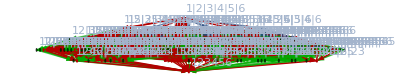

```mathematica
MobiusGraphDoubleGreen[K6Key,204484,allGraphs6]
```

```mathematica
Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},
VertexCount[g]==4&&EdgeCount[g]==4 
]&]
```

{360,354,352,336,334,328,282,280,274,256,120,118,112,94,40}

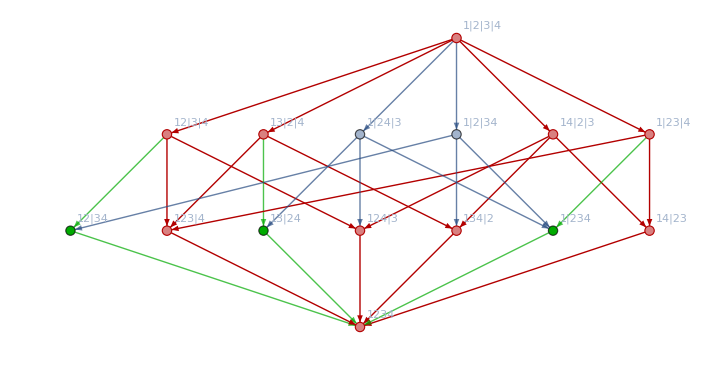
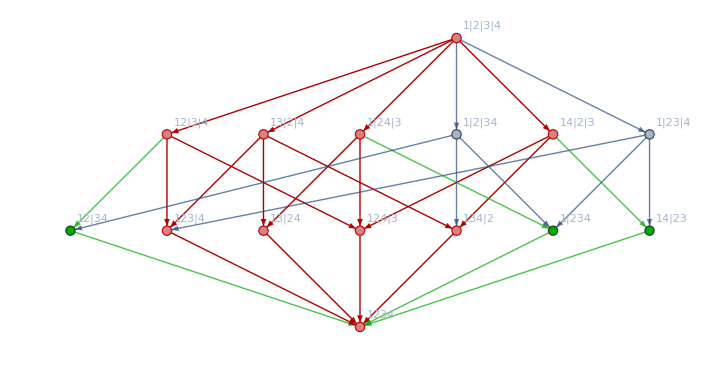
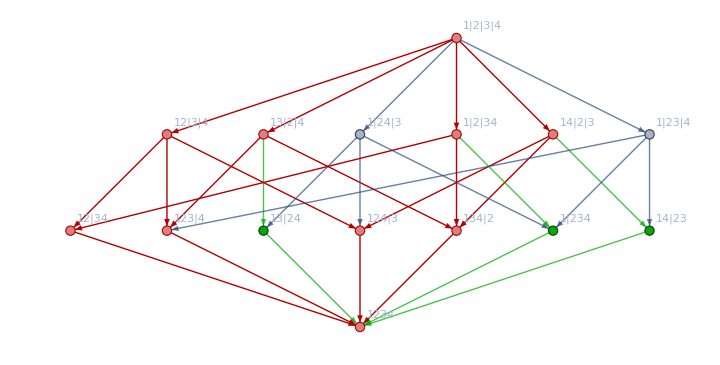
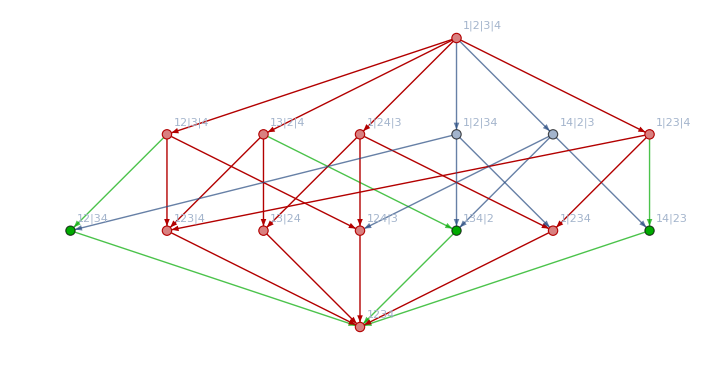
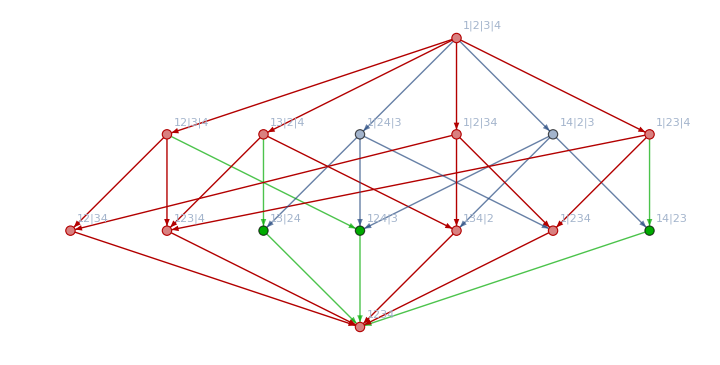
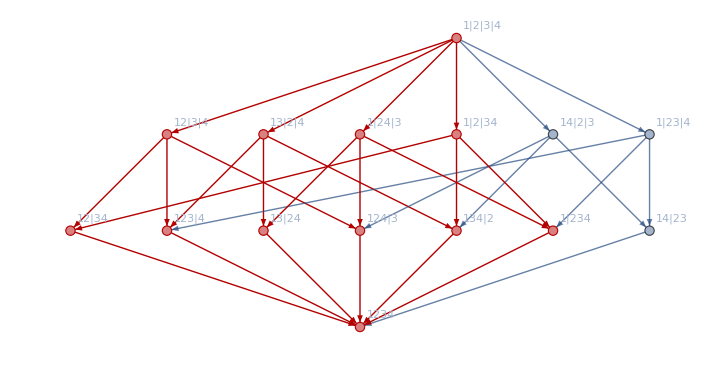
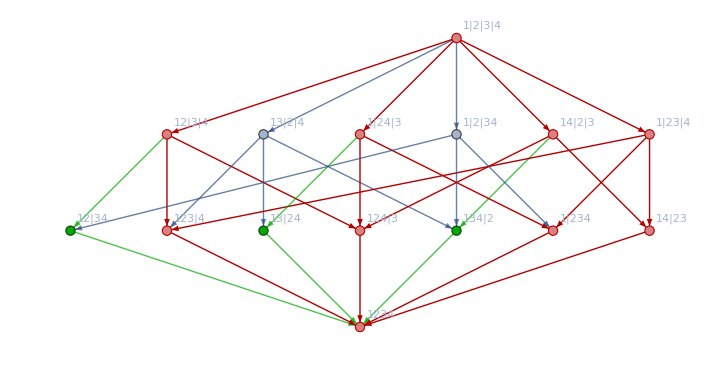
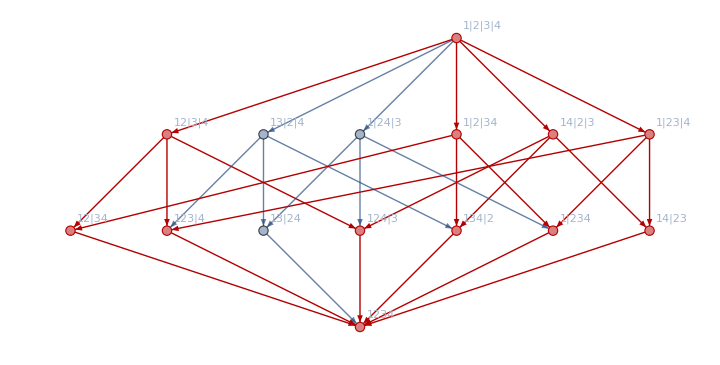
{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-}

```mathematica
Table[allGraphs4[k,"graph"]->MobiusGraphDoubleGreen[K4Key,k,allGraphs4],{k,Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},
VertexCount[g]==4&&EdgeCount[g]==4 
]&]}]
```

```mathematica
TableForm[
Table[allGraphs4[k,"graph"]->allGraphs4[k,"colofour"]/.repBase4Bare,{k,Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},
VertexCount[g]==4&&EdgeCount[g]==4 
]&]}]
]
```

-Graphics-→-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-

```mathematica
TableForm[
Table[allGraphs5[k,"graph"]->allGraphs5[k,"colofour"]/.repBase5Bare,{k,Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==7 
]&]}]
]
```

-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-
-Graphics-→-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},
VertexCount[g]==5&&EdgeCount[g]==3 &&Greater[ Length[FindClique[g,{3}]],0]
]&]
```

{26487,21951,20439,8757,7293,2917,333,273,109,13}

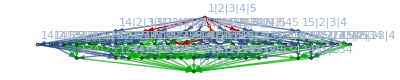

```mathematica
MobiusGraphDoubleGreen[K5Key,26487,allGraphs5]
```

```mathematica
Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},
VertexCount[g]==6&&EdgeCount[g]==3 &&Greater[ Length[FindClique[g,{3}]],0]
]&]
```

{6396975,5320971,4962303,4842747,2126007,1771551,1653399,708597,590493,236197,26487,21951,20439,8757,7293,2917,333,273,109,13}

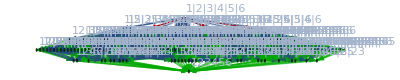

```mathematica
MobiusGraphDoubleGreen[K6Key,6396975,allGraphs6]
```